## Lesson

Arithmetic on lists:

```mathematica
{2,3,4}+{5,6,2}
```

{7,9,6}

Sort a list into order:

```mathematica
Sort[{5,7,1}]
```

{1,5,7}

Length of a list (number of elements):

```mathematica
Length[{3,3}]
```

2

Total of all elements in a list:

```mathematica
Total[{1,1,2}]
```

4

Count occurrences of an element:

```mathematica
Count[{3,2,3},3]
```

2

First element in a list:

```mathematica
First[{2,3}]
```

2

Last element in a list:

```mathematica
Last[{6,7,8}]
```

8

Particular part of a list, also written as {3, 1, 4}[[2]]:

```mathematica
Part[{3,1,4},2]
```

1

Take elements from the beginning of a list:

```mathematica
Take[{6,4,3,1},2]
```

{6,4}

Drop elements from the beginning of a list:

```mathematica
Drop[{6,4,3,1},2]
```

{3,1}

List of digits in a number:

```mathematica
IntegerDigits[1234]
```

{1,2,3,4}

## Questions

Q1. Make a list of the first 10 squares, in reverse order.

```mathematica
Reverse[Range[10]^2]
```

{100,81,64,49,36,25,16,9,4,1}

Q2. Find the total of the first 10 squares.

```mathematica
Total[Range[10]^2]
```

385

Q3. Make a plot of the first 10 squares, starting at 1.

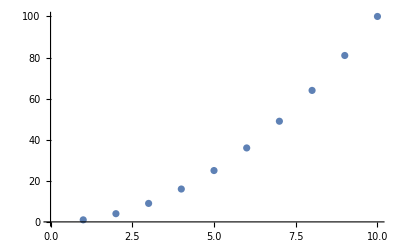

```mathematica
ListPlot[Range[10]^2]
```

Q4. Use Sort, Join and Range to create {1, 1, 2, 2, 3, 3, 4, 4}.

```mathematica
Sort[Join[Range[4],Range[4]]]
```

{1,1,2,2,3,3,4,4}

Q5. Use Range and + to make a list of numbers from 10 to 20, inclusive.

```mathematica
Range[11]+9
```

{10,11,12,13,14,15,16,17,18,19,20}

Q6. Make a combined list of the first 5 squares and cubes (numbers raised to the power 3), sorted into order.

```mathematica
Sort[Join[Range[5]^2,Range[5]^3]]
```

{1,1,4,8,9,16,25,27,64,125}

Q7. Find the number of digits in 2^128.

```mathematica
Length[IntegerDigits[2^128]]
```

39

Q8. Find the first digit of 2^32.

```mathematica
First[IntegerDigits[2^32]]
```

4

Q9. Find the first 10 digits in 2^100.

```mathematica
Take[IntegerDigits[2^100],10]
```

{1,2,6,7,6,5,0,6,0,0}

Q10. Find the largest digit that appears in 2^20.

```mathematica
Max[IntegerDigits[2^20]]
```

8

Q11. Find how many zeros appear in the digits of 2^1000.

```mathematica
Count[IntegerDigits[2^1000],0]
```

28

Q12. Use Part, Sort and IntegerDigits to find the second-smallest digit in 2^20.

```mathematica
Sort[IntegerDigits[2^20]][[2]]
```

1

Q13. Make a line plot of the sequence of digits that appear in 2^128.

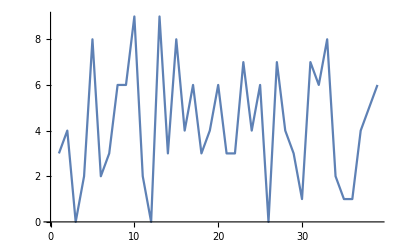

```mathematica
ListLinePlot[IntegerDigits[2^128]]
```

Q14. Use Take and Drop to get the sequence 11 through 20 from Range[100].

```mathematica
Drop[Take[Range[100],20],10]
```

{11,12,13,14,15,16,17,18,19,20}

## Extended Questions

+Q1. Make a list of the first 10 multiples of 3.

```mathematica
3Range[10]
```

{3,6,9,12,15,18,21,24,27,30}

+Q2. Make a list of the first 10 squares using only Range and Times.

```mathematica
Range[10]*Range[10]
```

{1,4,9,16,25,36,49,64,81,100}

+Q3. Find the last digit of 2^37.

```mathematica
Last[IntegerDigits[2^37]]
```

2

+Q4. Find the second-to-last digit of 2^37.

```mathematica
IntegerDigits[2^37][[-2]]
```

7

+Q5. Find the sum of all the digits of 3^126.

```mathematica
Total[IntegerDigits[3^126]]
```

234

+Q6. Make a pie chart of the sequence of digits that appear in 2^32.

```mathematica
PieChart[IntegerDigits[2^32]]
```

-Graphics-

+Q7. Make a list of pie charts for the sequence of digits in 2^20,20^40,2^60.

```mathematica
PieChart[IntegerDigits[2^(20#)]]&/@Range[3]
```

{-Graphics-,-Graphics-,-Graphics-}